```mathematica
𝒟=Bp Cp (1+((Bp (x) +Ap)/(1+d2))^2 1/(d1-2))^(-(1+d1)/2)
```

Bp Cp (1+(Ap+Bp x)^2/((-2+d1) (1+d2)^2))^(1/2 (-1-d1))

```mathematica
𝒟1=Solve[Eliminate[a==𝒟&&z==(Bp (x) +Ap)/(1+d2),{x}][[1]],a][[1,1,2]]//Quiet
```

(Bp Cp (1-z^2/(2-d1))^(-d1/2))/(√((-2+d1+z^2)/(-2+d1)))

```mathematica
up=(Bp (x) +Ap)/(1+d2)/.x->Q
```

(Ap+Bp Q)/(1+d2)

```mathematica
IntegrateRight=Integrate[z 𝒟1,{z,-Ap/Bp,up},Assumptions->{d1>2,d2<1,d2>-1,Cp∈Reals,z∈Reals,Ap∈Reals,Bp∈Reals,Q>-Ap/Bp}]
```

ConditionalExpression[(Bp Cp (-2+d1)^((1+d1)/2) (Bp^(-1+d1) (Ap^2+Bp^2 (-2+d1))^((1-d1)/2) (1+d2)-(1+d2)^d1 (Ap+Bp Q)^(1-d1) (1+((-2+d1) (1+d2)^2)/(Ap+Bp Q)^2)^((1-d1)/2)))/((-1+d1) (1+d2)), ]

```mathematica
Cp=Gamma[(d1+1)/2]/(Gamma[d1/2] √(π(d1-2)));
```

```mathematica
Ap=4 d2 Cp (d1-2)/(d1-1);
```

```mathematica
Bp=√(1+3 d2^2-Ap^2);
```

```mathematica
𝒟=Bp Cp (1+((Bp (x) +Ap)/(1-d2))^2 1/(d1-2))^(-(1+d1)/2)
```

Bp Cp (1+(Ap+Bp x)^2/((-2+d1) (1-d2)^2))^(1/2 (-1-d1))

```mathematica
𝒟1=Solve[Eliminate[a==𝒟&&z==(Bp (x) +Ap)/(1-d2),{x}][[1]],a][[1,1,2]]//Quiet
```

(Bp Cp (1-z^2/(2-d1))^(-d1/2))/(√((-2+d1+z^2)/(-2+d1)))

```mathematica
up=(Bp (x) +Ap)/(1-d2)/.x->Q
```

(Ap+Bp Q)/(1-d2)

```mathematica
IntegralLeft=Integrate[z 𝒟1,{z,-∞,-Ap/Bp},Assumptions->{d1>2,d2<1,d2>-1,Cp∈Reals,z∈Reals,Ap∈Reals,Bp∈Reals}]
```

-(Bp Cp (Ap^2+Bp^2 (-2+d1))^((1-d1)/2) (-2+d1)^((1+d1)/2) Abs[Bp]^(-1+d1))/(-1+d1)

```mathematica
IntegralLeftFull=IntegralLeft/.{Cp-> Gamma[(d1+1)/2]/(Gamma[d1/2] √(π(d1-2))),Ap-> 4 d2 Cp (d1-2)/(d1-1)/.Cp-> Gamma[(d1+1)/2]/(Gamma[d1/2] √(π(d1-2))),Bp-> √(1+3 d2^2-Ap^2)/.Ap-> 4 d2 Cp (d1-2)/(d1-1)/.Cp-> Gamma[(d1+1)/2]/(Gamma[d1/2] √(π(d1-2)))}
```

-1/((-1+d1) √π Gamma[d1/2])(-2+d1)^(-1/2+(1+d1)/2) Abs[1+3 d2^2-(16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2)/((-1+d1)^2 π Gamma[d1/2]^2)]^(1/2 (-1+d1)) Gamma[(1+d1)/2] √(1+3 d2^2-(16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2)/((-1+d1)^2 π Gamma[d1/2]^2)) ((16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2)/((-1+d1)^2 π Gamma[d1/2]^2)+(-2+d1) (1+3 d2^2-(16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2)/((-1+d1)^2 π Gamma[d1/2]^2)))^((1-d1)/2)

```mathematica
FullSimplify[IntegralLeftFull, Assumptions->{d1>2,d2<1,d2>-1}]
```

-π^(1/2 (-3+d1)) Abs[1+3 d2^2-(4 (-2+d1) d2^2 Gamma[1/2 (-1+d1)]^2)/(π Gamma[d1/2]^2)]^(1/2 (-1+d1)) ((-1+d1) Gamma[d1/2])^(-3+d1) Gamma[(1+d1)/2] ((-1+d1)^2 (1+3 d2^2) π Gamma[d1/2]^2-16 (-3+d1) d2^2 Gamma[(1+d1)/2]^2)^((1-d1)/2) √((-2+d1) ((-1+d1)^2 (1+3 d2^2) π Gamma[d1/2]^2-16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2))

```mathematica
Cp=.
Ap=.
Bp=.
```

```mathematica
f=PDF[ChiSquareDistribution[ν],x]
```

Piecewise[{{(2^(-ν/2) ⅇ^(-x/2) x^(-1+ν/2))/Gamma[ν/2], x>0}, {0, True}}]

```mathematica
Expectation[x,x\[Distributed]ChiSquareDistribution[ν]]
```

ν

```mathematica
f:=-x^2+9
```

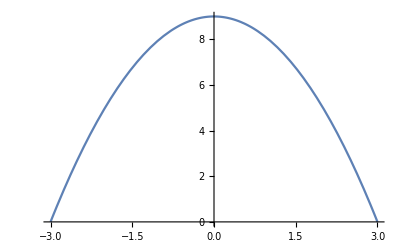

```mathematica
Plot[f,{x,-3,3}]
```

```mathematica
Integrate[x f,{x,-3,0}]/Integrate[f,{x,-3,0}]//N
```

-1.125

```mathematica
IntegrateRight
```

ConditionalExpression[(Bp Cp (-2+d1)^((1+d1)/2) (Bp^(-1+d1) (Ap^2+Bp^2 (-2+d1))^((1-d1)/2) (1+d2)-(1+d2)^d1 (Ap+Bp Q)^(1-d1) (1+((-2+d1) (1+d2)^2)/(Ap+Bp Q)^2)^((1-d1)/2)))/((-1+d1) (1+d2)), ]

```mathematica
PDF[StudentTDistribution[d1],x]
```

((d1/(d1+x^2))^((1+d1)/2))/(√d1 Beta[d1/2,1/2])